### My emission channel:

```mathematica
K0[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + Sqrt[1-Γ](KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
Ki[ajp_,aj_,i_,Γ_]:=Sqrt[Γ] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
SigmaTau[a1_,b1_,b2_,σ_]:= KroneckerDelta[σ,1]KroneckerDelta[a1,b1]+(1-KroneckerDelta[σ,1])KroneckerDelta[a1,b2]
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1))
```

### If I change Gamma to 1-exp(-Gamma):

```mathematica
K0Exp[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + (Exp[-Γ/2])(KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
KiExp[ajp_,aj_,i_,Γ_]:=Sqrt[(1-Exp[-Γ])] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
SigmaTau[a1_,b1_,b2_,σ_]:= KroneckerDelta[σ,1]KroneckerDelta[a1,b1]+(1-KroneckerDelta[σ,1])KroneckerDelta[a1,b2]
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1))
```

### Proceed to building bigger things...

```mathematica
K0K0dagExp[ajp_,aj_,bjp_,bj_,Γ_]:=K0Exp[ajp,aj,Γ]*K0Exp[bj,bjp,Γ]
KiKidagExp[ajp_,aj_,bjp_,bj_,i_,Γ_]:=KiExp[ajp,aj,i,Γ]*KiExp[bjp,bj,i,Γ]
```

```mathematica
wd[σ_,τ_,q_,Γ_,p_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]+Sum[KiKidag[a0p,a0,b0p,b0,i,Γ],{i,0,q-1}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ]+Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{p>0,q>0,Element[q,Integers]}]
w3a[a_,b_,c_,q_,Γ_,p_]:=wd[a,1,q,Γ,p] wd[b,1,q,Γ,p]wg[c,1,q^2]+wd[a,-1,q,Γ,p] wd[b,-1,q,Γ,p]wg[c,-1,q^2]
w3b[a_,b_,c_,q_,Γ_,p_]:=wd[1,a,q,Γ,p] wd[1,b,q,Γ,p]wg[1,c,q^2]+wd[-1,a,q,Γ,p] wd[-1,b,q,Γ,p]wg[-1,c,q^2]
```

```mathematica
Simplify[w3a[1,-1,1,q,Γ,p]-w3b[1,-1,1,q,Γ,p]]
```

1/15 Γ (Γ (10-2 Γ+Γ^2)-4 p Γ (10-2 Γ+Γ^2)+3 p^4 (5+4 Γ+Γ^2+2 Γ^3)-2 p^3 (10+23 Γ-4 Γ^2+7 Γ^3)+p^2 (10+63 Γ-12 Γ^2+11 Γ^3))

```mathematica
Simplify[Series[wd[1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wd[-1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wd[1,-1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wd[-1,-1,2,Γ,p],{Γ,0,1}]]
```

(4-8 p+6 p^2)+O[Γ]^2

(2-4 p+4 p^2)+O[Γ]^2

(2-4 p+4 p^2)-2 p^2 Γ+O[Γ]^2

(4-8 p+6 p^2)+(-4+8 p-6 p^2) Γ+O[Γ]^2

```mathematica
wdExp[σ_,τ_,q_,Γ_,p_]:=Sum[(K0K0dagExp[a0p,a0,b0p,b0,Γ]+Sum[KiKidagExp[a0p,a0,b0p,b0,i,Γ],{i,0,q-1}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dagExp[a1p,a1,b1p,b1,Γ]+Sum[KiKidagExp[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{p>0,q>0,Element[q,Integers]}]
```

```mathematica
w3aExp[a_,b_,c_,q_,Γ_,p_]:=wdExp[a,1,q,Γ,p] wdExp[b,1,q,Γ,p]wg[c,1,q^2]+wdExp[a,-1,q,Γ,p] wdExp[b,-1,q,Γ,p]wg[c,-1,q^2]
w3bExp[a_,b_,c_,q_,Γ_,p_]:=wdExp[1,a,q,Γ,p] wdExp[1,b,q,Γ,p]wg[1,c,q^2]+wdExp[-1,a,q,Γ,p] wdExp[-1,b,q,Γ,p]wg[-1,c,q^2]
```

```mathematica
Simplify[Series[wdExp[1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wdExp[-1,1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wdExp[1,-1,2,Γ,p],{Γ,0,1}]]
Simplify[Series[wdExp[-1,-1,2,Γ,p],{Γ,0,1}]]
```

(4-8 p+6 p^2)+O[Γ]^2

(2-4 p+4 p^2)+O[Γ]^2

(2-4 p+4 p^2)-2 p^2 Γ+O[Γ]^2

(4-8 p+6 p^2)+(-4+8 p-6 p^2) Γ+O[Γ]^2

```mathematica
wdtest[σ_,τ_,q_,Γ_,p_]:=
Which [σ==1&&τ==1,(1/2*q(1+q)+Γ^2) 2p^2-2q^2  p + q^2,
σ==-1&&τ==-1,(1-p)^2(1+2(q-1)(1-Γ)+(q-1)(q-2)(1-Γ)^2+(q-1)((1-Γ)^2+Γ^2) )+p^2(1+(q-1)((1-Γ)^2+Γ^2)),
σ==-1 &&τ==1,(1-2p+2p^2)(2Γ^2+q),
σ==1&&τ==-1, q-2q p + p^2(2q-2(q-1)(Γ-Γ^2))
]
w3test[a_,b_,c_,q_,Γ_,p_]:=wdtest[a,1,q,Γ,p] wdtest[b,1,q,Γ,p]wg[c,1,q^2]+wdtest[a,-1,q,Γ,p] wdtest[b,-1,q,Γ,p]wg[c,-1,q^2]
```

```mathematica
testFun[σ_,τ_,p_,q_,Γ_]:= Sum[K0K0dag[a0p,a0,b0p,b0,Γ]*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ],{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}]
(*testFun[σ_,τ_,p_,q_,Γ_]:= Sum[K0K0dag[a0p,a0,b0p,b0,Γ]*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*K0K0dag[a1p,a1,b1p,b1,Γ]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ],{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}]*)
```

```mathematica
K0[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + Sqrt[1-Γ](KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
Ki[ajp_,aj_,i_,Γ_]:=Sqrt[Γ] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
```

```mathematica
testFun[-1,-1,p,3,Γ]
testFun[-1,1,p,3,Γ]
testFun[1,-1,p,3,Γ]
testFun[1,1,p,3,Γ]
```

0

Γ+(1-Γ) Γ

2 (1-Γ) Γ

2 Γ+4 (1-Γ) Γ

```mathematica
Series[wd[-1,-1,2,Γ,p],{Γ,0,2}]
```

2 (2-4 p+3 p^2)-2 (2-4 p+3 p^2) Γ+(4-8 p+7 p^2) Γ^2+O[Γ]^3

```mathematica
Simplify[wd[-1,-1,3,Γ,p]]
Simplify[wd[-1,1,3,Γ,p]]
Simplify[wd[1,-1,3,Γ,p]]
FullSimplify[wd[1,1,3,Γ,p]]
```

9-12 Γ+6 Γ^2-6 p (3-4 Γ+2 Γ^2)+2 p^2 (6-8 Γ+5 Γ^2)

(1-2 p+2 p^2) (3+2 Γ^2)

3-6 p+p^2 (6-4 Γ+4 Γ^2)

9+2 p (-9+p (6+Γ^2))

```mathematica
w3test[]
```

q^2-2 p q^2+p^2 (q^2-2 (-2+Γ) Γ+q (1-2 Γ+2 Γ^2))

```mathematica
Simplify[4-8 p+p^2 (4-2 (-2+Γ) Γ+2 (1-2 Γ+2 Γ^2))]
```

4-8 p+2 p^2 (3+Γ^2)

```mathematica
Simplify[wdtest[1,1,3,Γ,p]]
Simplify[wdtest[1,-1,3,Γ,p]]
Simplify[wdtest[-1,1,3,Γ,p]]
FullSimplify[wdtest[-1,-1,3,Γ,p]]
```

9-18 p+2 p^2 (6+Γ^2)

3-6 p+p^2 (6-4 Γ+4 Γ^2)

(1-2 p+2 p^2) (3+2 Γ^2)

9+6 (-2+Γ) Γ-6 p (3+2 (-2+Γ) Γ)+2 p^2 (6+Γ (-8+5 Γ))

```mathematica
Collect[Simplify[wdtest[1,1,q,Γ,p]],q]
Collect[Simplify[wdtest[1,-1,q,Γ,p]],q]
Collect[Simplify[wdtest[-1,1,q,Γ,p]],q]
Collect[Simplify[wdtest[-1,-1,q,Γ,p]],q]
```

p^2 q+(1-2 p+p^2) q^2+2 p^2 Γ^2

2 p^2 (1-Γ) Γ+q (1-2 p+2 p^2+2 p^2 (-1+Γ) Γ)

(1-2 p+2 p^2) q+2 (1-2 p+2 p^2) Γ^2

(-1+p)^2 q^2 (-1+Γ)^2+2 p^2 Γ-2 p^2 Γ^2+q (-(-1+p)^2 (-2+Γ) Γ+p^2 (1-2 Γ+2 Γ^2))

```mathematica
testFun[-1,-1,p,4,Γ]
testFun[1,-1,p,4,Γ]
testFun[1,1,p,4,Γ]
```

0

3 (1-Γ) Γ

3 Γ+9 (1-Γ) Γ

```mathematica
w110/.{Γ->0,q->2}
```

-1/60 (4 (1-p)^2+2 p^2)^2+4/15 (1-2 p+2 p^2)^2

```mathematica
w000
```

((q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2)/(-1+q^4)-((q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2)))^2)/(q^2 (-1+q^4))

```mathematica
w000=w3test[1,1,1,q,Γ,p];
w001=w3test[1,1,-1,q,Γ,p];
w010=w3test[1,-1,1,q,Γ,p];
w100=w3test[-1,1,1,q,Γ,p];
w101=w3test[-1,1,-1,q,Γ,p];
w011=w3test[1,-1,-1,q,Γ,p];
w110=w3test[-1,-1,1,q,Γ,p];
w111=w3test[-1,-1,-1,q,Γ,p];
```

## Thermodynamic limit

```mathematica
n=100;
minFA1=Min[-(2n+1)Log[w110]-Log[w010]-Log[w100]-(2n+1)Log[w000],-n Log[w001]-(n+1)Log[w111]-(n+2)(Log[w010]+Log[w100])+2(n+1)Log[w000] -(2n+1)Log[w000]];
minFAB =Min[-(2n+2)(Log[w110]+Log[w111]+Log[w010]+Log[w100]-2Log[w000]),-(4n+4)(Log[w110]+2Log[w000])];
Fempty1=-(4n+4)Log[w000];
minFA2=Min[-(2n+1)Log[w110]-Log[w010]-Log[w100]-(2n+1)Log[w000],-(n+1) Log[w001]-(n+2)(Log[w010]+Log[w100])-n Log[w111]-(2n+1)Log[w000] ];
minFA3=Min[-2n Log[w110]-Log[w010]-Log[w100]-2n Log[w000],-n Log[w001]-n Log[w111]-(n+1)(Log[w010]+Log[w100])-2n Log[w000] ];
minFAB3 =Min[-(2n+1)(Log[w110]+Log[w111]+Log[w010]+Log[w100]),-(4n+2)(Log[w110]+2Log[w000])];
Fempty3=-(4n+2)Log[w000];
```

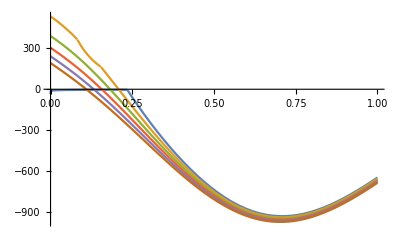

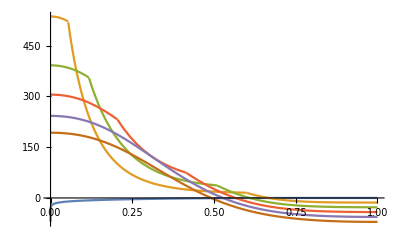

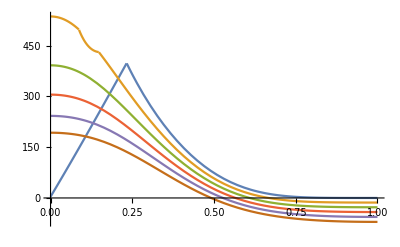

```mathematica
Plot[Evaluate[Table[{2minFA1-minFAB-Fempty1}/.{q->2,Γ->0.001*g},{g,0,100,20}]],
{p,0,1}]
Plot[Evaluate[Table[{2minFA2-minFAB-Fempty1}/.{q->2,Γ->0.001*g},{g,0,100,20}]],
{p,0,1}]
Plot[Evaluate[Table[{2minFA3-minFAB3-Fempty3}/.{q->2,Γ->0.001*g},{g,0,100,20}]],
{p,0,1}]
```

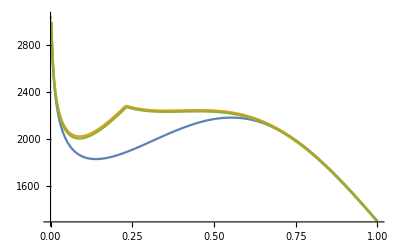

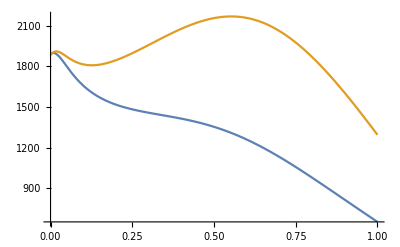

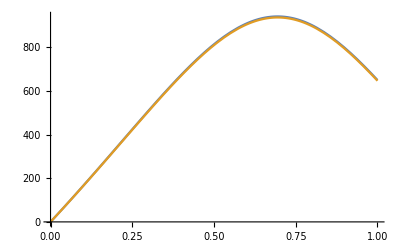

```mathematica
Plot[Evaluate[{2minFA1,2minFA2,2minFA3}/.{q->2,Γ->0.001}],
{p,0,1}]
Plot[Evaluate[{minFAB,minFAB3}/.{q->2,Γ->0.001}],
{p,0,1}]
Plot[Evaluate[{Fempty1,Fempty3}/.{q->2,Γ->0.001}],
{p,0,1}]
```

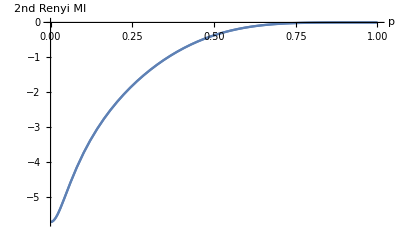

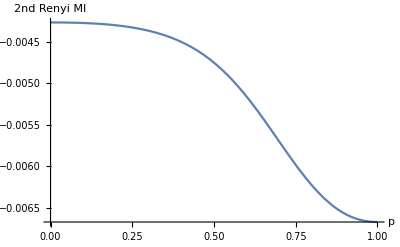

```mathematica
Plot[{-Log[w100*w010/(w110*w000)],-Log[w100*w010/(w110*w111)]}/.{q->2,Γ->0.001},
{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22}]
Plot[-2Log[w000/w111]/.{q->2,Γ->0.001},
{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22}]
```

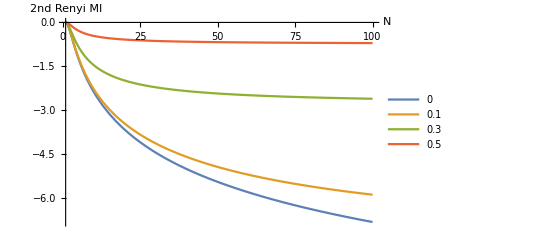

```mathematica
renyiMI2N = Plot[{-2Log[w100*w010/(w110*w000)]/.{q->2,p->0,Γ->(1/n)},-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1,Γ->(1/n)},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.3,Γ->(1/n)},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.5,Γ->(1/n)}},{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.1,0.3,0.5}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2N.png",Rasterize[renyiMI2N,ImageResolution->150]];
```

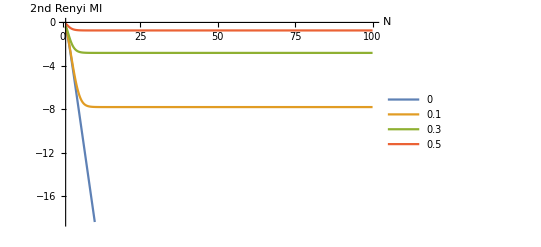

```mathematica
Plot[{-2Log[w100*w010/(w110*w000)]/.{q->2,p->0,Γ->(Exp[-n])},-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1,Γ->(Exp[-n])},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.3,Γ->(Exp[-n])},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.5,Γ->(Exp[-n])}},{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.1,0.3,0.5}]
```

```mathematica
Clear[p,Γ,q]
(w000)/.{q->2,p->0,Γ->0}
```

1

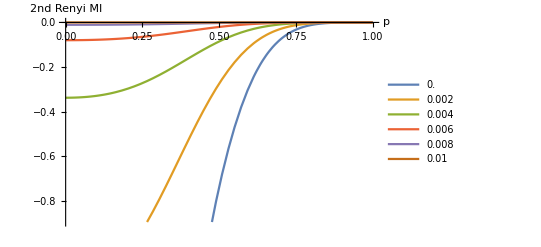

/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_area.png

```mathematica
renyiMI2 = Plot[Evaluate[Table[-2Log[w100*w010/(w110* w000)]/.{q->2,Γ->.01*g},{g,0,100,20}]],{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15],PlotRange->Automatic]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_area.png",Rasterize[renyiMI2,ImageResolution->150]]
```

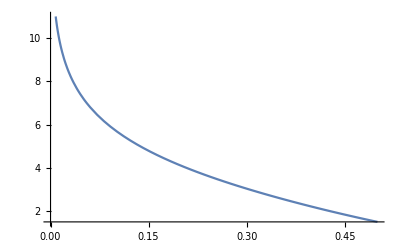

1

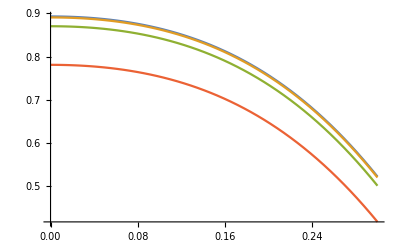

/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png

```mathematica
Plot[-Log[(w001/w111)]/.{q->2,Γ->0},{p,0,0.5}]
Clear[q]
Simplify[w111*w000/.{Γ->0,p->0}]
volc=Plot[{Max[(-2Log[(w101*w010)]+2Log[w000*w111]-4Log[2])/.{q->2,Γ->0},0],
Max[(-2Log[(w101*w010)]+2Log[w000*w111]-4Log[2])/.{q->2,Γ->0.001},0],
Max[(-2Log[(w101*w010)]+2Log[w000*w111]-4Log[2])/.{q->2,Γ->0.01},0],
Max[(-2Log[(w101*w010)]+2Log[w000*w111]-4Log[2])/.{q->2,Γ->0.05},0]},{p,0,0.3},PlotLegends->LineLegend[Automatic,{0,0.001,0.01,0.05},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["v_2(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->22}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png",Rasterize[volc,ImageResolution->150]]
```

```mathematica
Plot[{-2Log[w010 *w011/w110]/.{q->2,Γ->0.},-2Log[w010 *w011/w110]/.{q->2,Γ->0.001},-2Log[w010 *w011/w110]/.{q->2,Γ->0.01}},{p,0,1}]
```

```mathematica
w001/.{p->0,Γ->0}
Simplify[w110/.{p->0,Γ->0}]
Simplify[w000/.{p->0,Γ->0}]
Simplify[w010/.{p->0,Γ->0}]
Simplify[w011/.{p->0,Γ->0}]
```

0

0

1

q/(1+q^2)

q/(1+q^2)

0

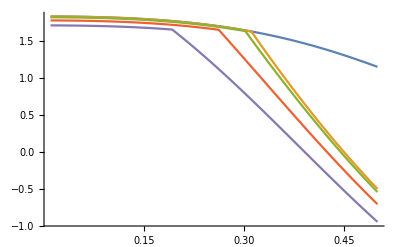

/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png

```mathematica
w001/.{p->0,Γ->0}
volc=Plot[{Min[-Log[w101*w010/w111/w000]]/.{q->2,Γ->0},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.001},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.01},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.046},
Min[-Log[w110/w111/w000],-Log[w101*w010/w111/w000]]/.{q->2,Γ->0.1}}
,{p,0.01,0.5}, PlotLegends->LineLegend[Automatic,{0,0.001,0.01,0.046,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["c(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->22}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/volumePref.png",Rasterize[volc,ImageResolution->150]]
```

Fix the system size nTot,

```mathematica
Shalf/.{p->0.1,Γ->0.1,q->2}
```

Log[1/(√π (15+h)!)2^(2 h) (-14+h) (-13+h) (-12+h) (-11+h) (-10+h) (-9+h) (-8+h) (-7+h) (-6+h) (-5+h) (-4+h) (-3+h) (-2+h) (-1+h) h (1/2 (-1+2 h))!]

```mathematica
45*6
```

270

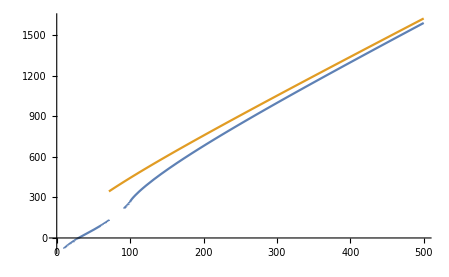

```mathematica
nTot=100;
Plot[{Log[nTot* Sum[Binomial[h,y]*Binomial[h,(y-nTot)]*Binomial[h,x]*Binomial[h,(x+nTot)],{y,nTot,h},{x,y+1,h}]]/.{h->nTot+xn}, 2Log[Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]]/.{h->nTot+xn}},{xn,0,5*nTot}]
```

50

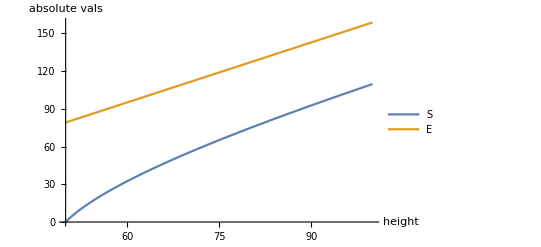

```mathematica
Clear[nTot]
nTot=50
deltaE =((h+nTot)*(-Log[w100])+(h-nTot)*(-Log[w101]) +h*nTot/2*(-Log[w111/w000]))/2;
Shalf = Log[Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]];
Stot =Log[nTot* Sum[Binomial[h,y]*Binomial[h,(y-nTot)]*Binomial[h,x]*Binomial[h,(x-nTot)],{y,nTot,h},{x,y,nTot}]]
Plot[{Shalf,deltaE/.{p->0.1,Γ->0.01,q->2}},{h,nTot,2*nTot},AxesLabel->{"height","absolute vals"},PlotLegends->{"S","E"}]
```

```mathematica
SABt = Log[w110]/Log[w111];
SAt = 1/n*(-n Log[w101]-n ^2/2 Log[w111] )/(n/2 * (-Log[w111])+2*(-Log[w101]-Log[2]));
v2 = Max[-2Log[(w101*w010/(w111*w000))]-2Log[2],0];
```

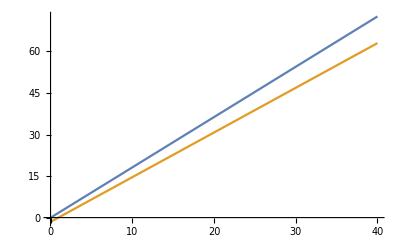

```mathematica
Plot[{(-2 Log[w101]-2Log[2])(t-SAt)+Log[w000](t-SABt)/.{p->0.1,Γ->0.1,q->2},-Log[w101]*(t-SAt)/.{p->0.1,Γ->0.2,q->2}},{t,0,40}]
```

50

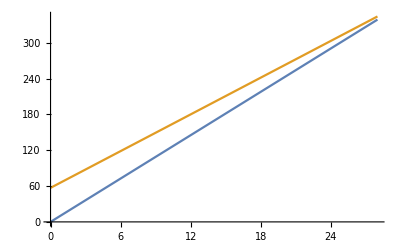

```mathematica
n=50
Plot[{-n/2*t*Log[w111]-t*Log[w010]/.{Γ->0.01,q->2,p->0.1},-(n*t/2-(n-1)^2/8-n)Log[w000]-n^2/8Log[w111]-n Log[w100]/.{Γ->0.01,q->2,p->0.1}},{t,0,n/2+3}]
```

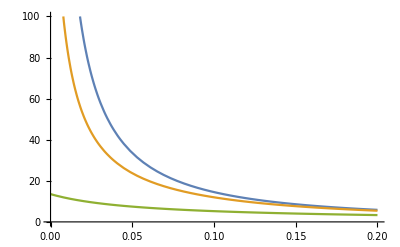

/Users/cathy/Google Drive/Random circuits/Pics/S_ABsatTime.png

```mathematica
SABsatTime = Plot[{Log[w110]/Log[w111]/.{Γ->0.001,q->2},Log[w110]/Log[w111]/.{Γ->0.01,q->2},Log[w110]/Log[w111]/.{Γ->0.1,q->2}},{p,0,0.2},PlotLegends->LineLegend[Automatic,{0.001,0.01,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["t^*(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->22},PlotRange->{{0,0.2},{0,100}}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/S_ABsatTime.png",Rasterize[SABsatTime,ImageResolution->150]]
```

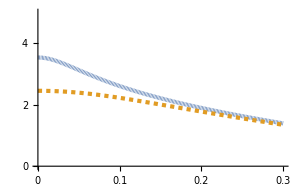

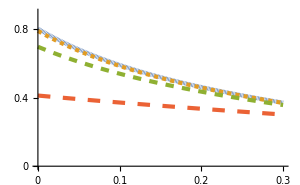

/Users/cathy/Google Drive/Random circuits/Pics/S_AsatTime.png

```mathematica
Needs["MaTeX`"]
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,11,3}],
Table[AbsoluteThickness[3],{i,1,4}]}];
n=10000000;
SAsatTime = Show[Plot[
{Γ*n/2Log[w110/w000]/(n/2Log[w111/w000]+Log[w100*w010])/.{Γ->0.001,q->2},Γ*n/2Log[w110/w000]/(n/2Log[w111/w000]+Log[w100*w010])/.{Γ->0.01,q->2}},{p,0,0.3},(*PlotLegends->LineLegend[Automatic,{0 ,0.001,0.01,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],*)
PlotStyle->dashThick,
PlotRange->{{0,0.3},{0,5}},
Ticks->{{0,0.1,0.2,0.3},{0,1,2,3,4}},
PlotLegends->LineLegend[Automatic,{"10^-4","10^-3","10^-2"},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2.5],LegendMarkerSize->23],
AxesLabel->{MaTeX["p",Magnification->2.5],
MaTeX[" \\Gamma t^*_A(p,\\Gamma)",Magnification->2.5]},LabelStyle->{FontSize->24}],ImageSize->300]
n=250;
SAsatTime2 = Show[Plot[{1/n(-(n/2-1)^2/2*Log[w111]+  (n/2+1)^2/2*Log[w000]-n*Log[w010])/(-(n/2-1) * Log[w111]+n/2*Log[w000]-Log[w010*w011]-Log[2])/.{Γ->0.,q->2},
1/n(-(n/2-1)^2/2*Log[w111]+  (n/2+1)^2/2*Log[w000]-n*Log[w010])/(-(n/2-1) * Log[w111]+n/2*Log[w000]-Log[w010*w011]-Log[2])/.{Γ->0.0001,q->2},1/n(-(n/2-1)^2/2*Log[w111]+  (n/2+1)^2/2*Log[w000]-n*Log[w010])/(-(n/2-1) * Log[w111]+n/2*Log[w000]-Log[w010*w011]-Log[2])/.{Γ->0.001,q->2},
1/n(-(n/2-1)^2/2*Log[w111]+  (n/2+1)^2/2*Log[w000]-n*Log[w010])/(-(n/2-1) * Log[w111]+n/2*Log[w000]-Log[w010*w011]-Log[2])/.{Γ->0.01,q->2}},
{p,0,.3},
PlotStyle->dashThick,
Ticks->{{0,0.1,0.2,0.3},{0,.2,.4,.6,.8}},
PlotLegends->LineLegend[Automatic,{"0","10^-4","10^-3","10^-2"},Spacings->0.05,LegendLabel->MaTeX["\\Gamma",Magnification->2],LegendMarkerSize->30],
AxesLabel->{MaTeX["p",Magnification->2],MaTeX["t^*_A(p,\\Gamma)/N",Magnification->2]},LabelStyle->{FontSize->20},PlotRange->{{0,0.3},{0,.9}}],ImageSize->300]
Export["/Users/cathy/Google Drive/Random circuits/Pics/S_AsatTime.png",Rasterize[SAsatTime2,ImageResolution->150]]
```

```mathematica
Collect[Expand[-(n/2-1)^2/2*Log[w111]+  (n/2+1)^2/2*Log[w000]-n*Log[w010]],n]
```

1/2 Log[((q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2)/(-1+q^4)-((q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2)))^2)/(q^2 (-1+q^4))]+n^2 (1/8 Log[((q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2)/(-1+q^4)-((q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2)))^2)/(q^2 (-1+q^4))]-1/8 Log[-((1-2 p+2 p^2)^2 (q+2 Γ^2)^2)/(q^2 (-1+q^4))+((p^2 (1+(-1+q) ((1-Γ)^2+Γ^2))+(1-p)^2 (1+2 (-1+q) (1-Γ)+(-2+q) (-1+q) (1-Γ)^2+(-1+q) ((1-Γ)^2+Γ^2)))^2)/(-1+q^4)])+n (1/2 Log[((q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2)/(-1+q^4)-((q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2)))^2)/(q^2 (-1+q^4))]-Log[((1-2 p+2 p^2) (q+2 Γ^2) (q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2)))/(-1+q^4)-1/(q^2 (-1+q^4))(q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2))) (p^2 (1+(-1+q) ((1-Γ)^2+Γ^2))+(1-p)^2 (1+2 (-1+q) (1-Γ)+(-2+q) (-1+q) (1-Γ)^2+(-1+q) ((1-Γ)^2+Γ^2)))]+1/2 Log[-((1-2 p+2 p^2)^2 (q+2 Γ^2)^2)/(q^2 (-1+q^4))+((p^2 (1+(-1+q) ((1-Γ)^2+Γ^2))+(1-p)^2 (1+2 (-1+q) (1-Γ)+(-2+q) (-1+q) (1-Γ)^2+(-1+q) ((1-Γ)^2+Γ^2)))^2)/(-1+q^4)])-1/2 Log[-((1-2 p+2 p^2)^2 (q+2 Γ^2)^2)/(q^2 (-1+q^4))+((p^2 (1+(-1+q) ((1-Γ)^2+Γ^2))+(1-p)^2 (1+2 (-1+q) (1-Γ)+(-2+q) (-1+q) (1-Γ)^2+(-1+q) ((1-Γ)^2+Γ^2)))^2)/(-1+q^4)]

```mathematica
Clear[n]
Series[(-(n/2-1)^2/2*Log[w111]+  (n/2+1)^2/2*Log[w000]-n*Log[w010])/(-(n/2-1) * Log[w111]+n/2*Log[w000]-Log[w010*w011]-Log[2]),{Γ,0,1}]
Series[(-(n-2)^2/2 Log[w111]+n^2/2*Log[w000]-(2n-4)*Log[w100]-2Log[w110] )/(n * (-Log[w111/w000])),{Γ,0,1}]
```

(-n Log[(p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)/(1+q^2)]-1/8 (-2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/8 (2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)])/(-Log[2]-Log[((p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)^2)/((1+q^2)^2)]-1/2 (-2+n) Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/2 n Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)])+((-(2 n (1-2 p+3 p^2))/((1-2 p+2 p^2) q (1+q))+((2+n)^2 (p^2-2 p^3+2 p^4))/(2 q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3))+(2 (-1+n/2)^2 q (p^2+q-2 p q+p^2 q)^2)/((1+q+q^2+q^3) (-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4))))/(-Log[2]-Log[((p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)^2)/((1+q^2)^2)]-1/2 (-2+n) Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/2 n Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)])-(((2 (1-2 p+3 p^2) (-1+q))/((1-2 p+2 p^2) q)+(2 n (p^2-2 p^3+2 p^4))/(q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3))-(4 (1-n/2) q (p^2+q-2 p q+p^2 q)^2)/((1+q+q^2+q^3) (-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)))) (-n Log[(p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)/(1+q^2)]-1/8 (-2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/8 (2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)]))/(-Log[2]-Log[((p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)^2)/((1+q^2)^2)]-1/2 (-2+n) Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/2 n Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)])^2) Γ+O[Γ]^2

(q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3) (-2 (-2+n) Log[(p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)/(1+q^2)]-2 Log[(p^4+2 p^2 q-4 p^3 q+3 p^4 q)/(1+q+q^2+q^3)]-1/2 (-2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/2 n^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)]))/(4 n (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4) Γ)+1/n((q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3) (-(4 (-2+n) (1-2 p+3 p^2))/((1-2 p+2 p^2) q (1+q))-(8 (p^2+q-2 p q+p^2 q)^2)/(p^2 q (p^2+2 q-4 p q+3 p^2 q))+(2 n^2 (p^2-2 p^3+2 p^4))/(q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3))+(2 (-2+n)^2 q (p^2+q-2 p q+p^2 q)^2)/((1+q+q^2+q^3) (-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)))))/(4 (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4))-((2 p^4-8 p^5+16 p^6-16 p^7+8 p^8+2 q-16 p q+66 p^2 q-172 p^3 q+306 p^4 q-376 p^5 q+312 p^6 q-160 p^7 q+40 p^8 q+2 q^2-16 p q^2+64 p^2 q^2-160 p^3 q^2+270 p^4 q^2-312 p^5 q^2+240 p^6 q^2-112 p^7 q^2+26 p^8 q^2+2 q^3-16 p q^3+60 p^2 q^3-136 p^3 q^3+208 p^4 q^3-224 p^5 q^3+178 p^6 q^3-100 p^7 q^3+30 p^8 q^3+9 p^2 q^4-54 p^3 q^4+153 p^4 q^4-252 p^5 q^4+248 p^6 q^4-136 p^7 q^4+32 p^8 q^4+3 q^5-24 p q^5+90 p^2 q^5-204 p^3 q^5+305 p^4 q^5-308 p^5 q^5+202 p^6 q^5-76 p^7 q^5+12 p^8 q^5+2 p^2 q^6-12 p^3 q^6+24 p^4 q^6-16 p^5 q^6-5 p^6 q^6+10 p^7 q^6-3 p^8 q^6-6 p^2 q^7+36 p^3 q^7-87 p^4 q^7+108 p^5 q^7-72 p^6 q^7+24 p^7 q^7-3 p^8 q^7-2 q^8+16 p q^8-53 p^2 q^8+94 p^3 q^8-95 p^4 q^8+52 p^5 q^8-11 p^6 q^8-2 p^7 q^8+p^8 q^8+q^9-8 p q^9+28 p^2 q^9-56 p^3 q^9+70 p^4 q^9-56 p^5 q^9+28 p^6 q^9-8 p^7 q^9+p^8 q^9) (-2 (-2+n) Log[(p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)/(1+q^2)]-2 Log[(p^4+2 p^2 q-4 p^3 q+3 p^4 q)/(1+q+q^2+q^3)]-1/2 (-2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/2 n^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)]))/(8 (-1+q) (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4)^2))+1/n(-(((2 p^4-8 p^5+16 p^6-16 p^7+8 p^8+2 q-16 p q+66 p^2 q-172 p^3 q+306 p^4 q-376 p^5 q+312 p^6 q-160 p^7 q+40 p^8 q+2 q^2-16 p q^2+64 p^2 q^2-160 p^3 q^2+270 p^4 q^2-312 p^5 q^2+240 p^6 q^2-112 p^7 q^2+26 p^8 q^2+2 q^3-16 p q^3+60 p^2 q^3-136 p^3 q^3+208 p^4 q^3-224 p^5 q^3+178 p^6 q^3-100 p^7 q^3+30 p^8 q^3+9 p^2 q^4-54 p^3 q^4+153 p^4 q^4-252 p^5 q^4+248 p^6 q^4-136 p^7 q^4+32 p^8 q^4+3 q^5-24 p q^5+90 p^2 q^5-204 p^3 q^5+305 p^4 q^5-308 p^5 q^5+202 p^6 q^5-76 p^7 q^5+12 p^8 q^5+2 p^2 q^6-12 p^3 q^6+24 p^4 q^6-16 p^5 q^6-5 p^6 q^6+10 p^7 q^6-3 p^8 q^6-6 p^2 q^7+36 p^3 q^7-87 p^4 q^7+108 p^5 q^7-72 p^6 q^7+24 p^7 q^7-3 p^8 q^7-2 q^8+16 p q^8-53 p^2 q^8+94 p^3 q^8-95 p^4 q^8+52 p^5 q^8-11 p^6 q^8-2 p^7 q^8+p^8 q^8+q^9-8 p q^9+28 p^2 q^9-56 p^3 q^9+70 p^4 q^9-56 p^5 q^9+28 p^6 q^9-8 p^7 q^9+p^8 q^9) (-(4 (-2+n) (1-2 p+3 p^2))/((1-2 p+2 p^2) q (1+q))-(8 (p^2+q-2 p q+p^2 q)^2)/(p^2 q (p^2+2 q-4 p q+3 p^2 q))+(2 n^2 (p^2-2 p^3+2 p^4))/(q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3))+(2 (-2+n)^2 q (p^2+q-2 p q+p^2 q)^2)/((1+q+q^2+q^3) (-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)))))/(8 (-1+q) (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4)^2))+(q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3) ((16 (p^2+q-2 p q+p^2 q)^4)/(q^2 (p^4+2 p^2 q-4 p^3 q+3 p^4 q)^2)+1/2 (-4+2 n) ((4 (p^2-2 p^3+3 p^4+q-4 p q+8 p^2 q-8 p^3 q+3 p^4 q)^2 (1+q^2)^2)/(q^2 (p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)^2 (1+q+q^2+q^3)^2)-(2 (1+q^2) ((4 p^4+2 p^2 q-4 p^3 q-6 p^4 q-q^2+4 p q^2-13 p^2 q^2+18 p^3 q^2-8 p^4 q^2)/(q^2 (1+q+q^2+q^3))+(2 (1-2 p+2 p^2) (2 p^2 q+q^2-2 p q^2+p^2 q^2))/(-1+q^4)))/(p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q))+1/4 n^2 (-(16 p^4 (1-2 p+2 p^2)^2)/(q^2 (1+q+q^2+q^3)^2 (-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4))^2)+(2 (-(4 (-p^4+p^2 q-2 p^3 q+3 p^4 q))/(q^2 (1+q+q^2+q^3))+(4 p^2 (q^2-2 p q^2+p^2 q (1+q)))/(-1+q^4)))/(-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)))-(2 (1+q+q^2+q^3) ((4 (1-2 p+2 p^2)^2 q)/(-1+q^4)+(-(-2 p^2 (-1+q)-2 (-1+p)^2 (-q+q^2))^2-2 (p^2 q+(-1+p)^2 q^2) (2 p^2 (-1+q)+(-1+p)^2 (-q+q^2)))/(q^2 (-1+q^4))))/(p^4+2 p^2 q-4 p^3 q+3 p^4 q)+1/4 (-2+n)^2 ((16 q^2 (p^2+q-2 p q+p^2 q)^4)/((1+q+q^2+q^3)^2 (-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4))^2)-(2 (-(4 (1-2 p+2 p^2)^2)/(q (-1+q^4))+((-2 p^2 (-1+q)-2 (-1+p)^2 (-q+q^2))^2+2 (p^2 q+(-1+p)^2 q^2) (2 p^2 (-1+q)+(-1+p)^2 (-q+q^2)))/(-1+q^4)))/(-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)))))/(4 (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4))+(q (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3) ((2 p^4-8 p^5+16 p^6-16 p^7+8 p^8+2 q-16 p q+66 p^2 q-172 p^3 q+306 p^4 q-376 p^5 q+312 p^6 q-160 p^7 q+40 p^8 q+2 q^2-16 p q^2+64 p^2 q^2-160 p^3 q^2+270 p^4 q^2-312 p^5 q^2+240 p^6 q^2-112 p^7 q^2+26 p^8 q^2+2 q^3-16 p q^3+60 p^2 q^3-136 p^3 q^3+208 p^4 q^3-224 p^5 q^3+178 p^6 q^3-100 p^7 q^3+30 p^8 q^3+9 p^2 q^4-54 p^3 q^4+153 p^4 q^4-252 p^5 q^4+248 p^6 q^4-136 p^7 q^4+32 p^8 q^4+3 q^5-24 p q^5+90 p^2 q^5-204 p^3 q^5+305 p^4 q^5-308 p^5 q^5+202 p^6 q^5-76 p^7 q^5+12 p^8 q^5+2 p^2 q^6-12 p^3 q^6+24 p^4 q^6-16 p^5 q^6-5 p^6 q^6+10 p^7 q^6-3 p^8 q^6-6 p^2 q^7+36 p^3 q^7-87 p^4 q^7+108 p^5 q^7-72 p^6 q^7+24 p^7 q^7-3 p^8 q^7-2 q^8+16 p q^8-53 p^2 q^8+94 p^3 q^8-95 p^4 q^8+52 p^5 q^8-11 p^6 q^8-2 p^7 q^8+p^8 q^8+q^9-8 p q^9+28 p^2 q^9-56 p^3 q^9+70 p^4 q^9-56 p^5 q^9+28 p^6 q^9-8 p^7 q^9+p^8 q^9)^2/(4 (-1+q)^2 q^2 (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3)^2 (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4)^2)-(-4 p^6+24 p^7-72 p^8+128 p^9-144 p^10+96 p^11-32 p^12-6 p^4 q+48 p^5 q-188 p^6 q+456 p^7 q-744 p^8 q+832 p^9 q-624 p^10 q+288 p^11 q-64 p^12 q-12 p^10 q^2+24 p^11 q^2-24 p^12 q^2+18 p^4 q^3-144 p^5 q^3+564 p^6 q^3-1368 p^7 q^3+2208 p^8 q^3-2400 p^9 q^3+1716 p^10 q^3-744 p^11 q^3+168 p^12 q^3+33 p^2 q^4-330 p^3 q^4+1617 p^4 q^4-5016 p^5 q^4+10812 p^6 q^4-16824 p^7 q^4+19092 p^8 q^4-15600 p^9 q^4+8796 p^10 q^4-3096 p^11 q^4+504 p^12 q^4+15 q^5-180 p q^5+1074 p^2 q^5-4140 p^3 q^5+11391 p^4 q^5-23448 p^5 q^5+36876 p^6 q^5-44472 p^7 q^5+40632 p^8 q^5-27264 p^9 q^5+12648 p^10 q^5-3600 p^11 q^5+486 p^12 q^5+12 q^6-144 p q^6+864 p^2 q^6-3360 p^3 q^6+9276 p^4 q^6-18912 p^5 q^6+28944 p^6 q^6-33312 p^7 q^6+28560 p^8 q^6-17856 p^9 q^6+7872 p^10 q^6-2304 p^11 q^6+356 p^12 q^6+12 q^7-144 p q^7+816 p^2 q^7-2880 p^3 q^7+7092 p^4 q^7-12960 p^5 q^7+18276 p^6 q^7-20376 p^7 q^7+18108 p^8 q^7-12624 p^9 q^7+6492 p^10 q^7-2136 p^11 q^7+322 p^12 q^7+48 p^2 q^8-480 p^3 q^8+2256 p^4 q^8-6528 p^5 q^8+12840 p^6 q^8-17904 p^7 q^8+17820 p^8 q^8-12336 p^9 q^8+5559 p^10 q^8-1422 p^11 q^8+147 p^12 q^8+12 q^9-144 p q^9+816 p^2 q^9-2880 p^3 q^9+7038 p^4 q^9-12528 p^5 q^9+16552 p^6 q^9-16080 p^7 q^9+11025 p^8 q^9-4868 p^9 q^9+1086 p^10 q^9+12 p^11 q^9-41 p^12 q^9-60 p^4 q^10+480 p^5 q^10-1690 p^6 q^10+3420 p^7 q^10-4350 p^8 q^10+3560 p^9 q^10-1830 p^10 q^10+540 p^11 q^10-70 p^12 q^10-24 p^2 q^11+240 p^3 q^11-1080 p^4 q^11+2880 p^5 q^11-5040 p^6 q^11+6048 p^7 q^11-5040 p^8 q^11+2880 p^9 q^11-1080 p^10 q^11+240 p^11 q^11-24 p^12 q^11-4 q^12+48 p q^12-261 p^2 q^12+850 p^3 q^12-1845 p^4 q^12+2808 p^5 q^12-3066 p^6 q^12+2412 p^7 q^12-1350 p^8 q^12+520 p^9 q^12-129 p^10 q^12+18 p^11 q^12-p^12 q^12+q^13-12 p q^13+66 p^2 q^13-220 p^3 q^13+495 p^4 q^13-792 p^5 q^13+924 p^6 q^13-792 p^7 q^13+495 p^8 q^13-220 p^9 q^13+66 p^10 q^13-12 p^11 q^13+p^12 q^13)/(3 (-1+q) q^2 (1-4 p+8 p^2-8 p^3+4 p^4+q-4 p q+8 p^2 q-8 p^3 q+4 p^4 q+q^2-4 p q^2+8 p^2 q^2-8 p^3 q^2+3 p^4 q^2+q^3-4 p q^3+6 p^2 q^3-4 p^3 q^3+p^4 q^3)^2 (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4))) (-2 (-2+n) Log[(p^2-2 p^3+2 p^4+q-4 p q+7 p^2 q-6 p^3 q+2 p^4 q)/(1+q^2)]-2 Log[(p^4+2 p^2 q-4 p^3 q+3 p^4 q)/(1+q+q^2+q^3)]-1/2 (-2+n)^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((p^2 q+(-1+p)^2 q^2)^2)/(-1+q^4)]+1/2 n^2 Log[-((1-2 p+2 p^2)^2)/(-1+q^4)+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)]))/(4 (p^2-2 p^3+2 p^4+p^4 q^2+2 p^2 q^3-4 p^3 q^3+2 p^4 q^3+q^4-4 p q^4+6 p^2 q^4-4 p^3 q^4+p^4 q^4))) Γ+O[Γ]^2

```mathematica
plots1=GraphicsRow[{SAsatTime,SAsatTime2},Spacings->1,ImageSize->{800,230}]
```

-Graphics-

/Users/cathy/Google Drive/Random circuits/Pics/S_AsatTime.png

10000

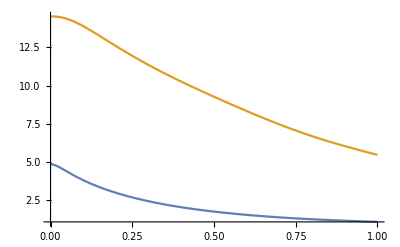

```mathematica
n=10000
tAmin = Solve[1/2(t-1)^2 (-Log[w111/w000])-t(Log[w100*w010/(2 w000)]+2Log[w000])-2Log[w000]+(n/2-1)Log[w110] +Log[w010]+Log[w100]==0,t][[1]][[1]];
Plot[{Γ t/.{tAmin/.{Γ->0.001,q->2},Γ->0.001},Γ t/.{tAmin/.{Γ->0.01,q->2},Γ->0.01}},{p,0,1},PlotRange->Full,PlotLegends->LineLegend[Automatic,{"10^-3","10^-2"},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2.5],LegendMarkerSize->23],
AxesLabel->{MaTeX["p",Magnification->2.5],MaTeX["\\Gamma t^*_A(p,\\Gamma)",Magnification->2.5]},LabelStyle->{FontSize->24}]
```

-Graphics-

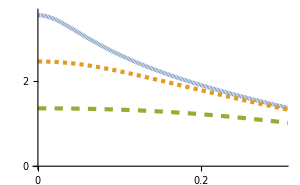

```mathematica
Show[SAsatTime]
Show[SABsatTime ]
```

10000000

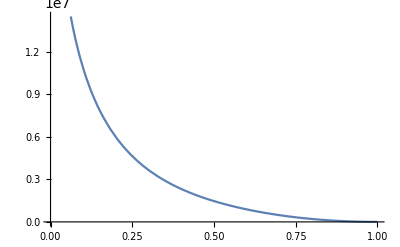

```mathematica
n=10000000
Plot[Log[w110/w000]/(Log[w111/w000]+2/n Log[w100*w010])/.{Γ->0,q->2},
{p,0,1}]
```

10000000

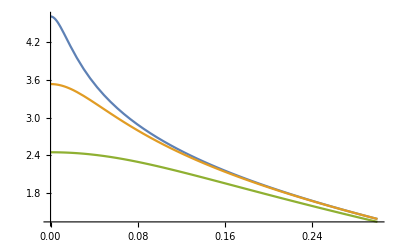

```mathematica
n=10000000
Plot[{Γ*n/2Log[w110/w000]/(n/2Log[w111/w000]+ Log[w100*w010])/.{Γ->0.0001,q->2},Γ*n/2Log[w110/w000]/(n/2Log[w111/w000]+Log[w100*w010])/.{Γ->0.001,q->2},
Γ*n/2Log[w110/w000]/(n/2Log[w111/w000]+Log[w100*w010])/.{Γ->0.01,q->2}},
{p,0,0.3}]
```

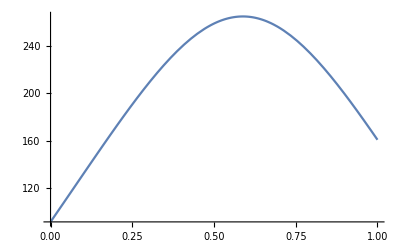

```mathematica
Plot[deltaE-Shalf/.{h->nTot,Γ->0.0,q->2},{p,0,1}]
```

```mathematica
Plot[-nTot*Log[w110]/.{p->0.,Γ->0.0,q->2},{h,nTot,nTot*2}]
```

Plot[-nTot Log[w110]/.{p→0.,Γ→0.,q→2},{h,nTot,nTot 2}]

```mathematica
w000/.{p->0,Γ->0.0,q->2}
```

1.

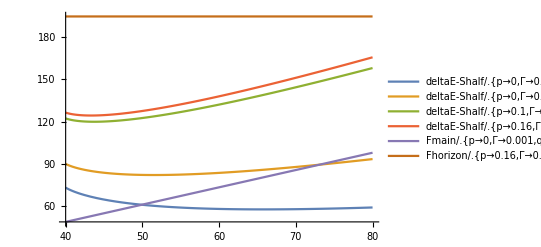

```mathematica
nTot=40;
deltaE =(h+nTot)*(-Log[w100])+(h-nTot)*(-Log[w101]) +h*nTot/2*(-Log[w111/w000]);
Shalf = Log[Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]];
deltaEtot = 2 (h+nTot)*(-Log[w100])+2(h-nTot)*(-Log[w101]) +h*nTot*(-Log[w111/w000]);
Stot =Log[nTot/2]+ 2Log[nTot  * Sum[Binomial[h,y]*Binomial[h,(y-nTot)],{y,nTot,h}]];
Fmain = h(-Log[w100*w101]-nTot*(Log[w111/w000])-Log[2]);
Fhorizon=-nTot*Log[w110];
Plot[{deltaE-Shalf/.{p->0,Γ->0.0,q->2},deltaE-Shalf/.{p->0,Γ->0.01,q->2},deltaE-Shalf/.{p->0.1,Γ->0.01,q->2},deltaE-Shalf/.{p->0.16,Γ->0.001,q->2},Fmain/.{p->0,Γ->0.001,q->2},Fhorizon/.{p->0.16,Γ->0.01,q->2}},{h,nTot,nTot*2},PlotLegends->"Expressions",AxesLabel->{MaTeX[h,Magnification->2],MaTeX[F,Magnification->2]}]
(*FindMinimum[deltaE+Shalf/.{p->0.1,Γ->0.01,q->2},{h,nTot/2}]*)
```

Null

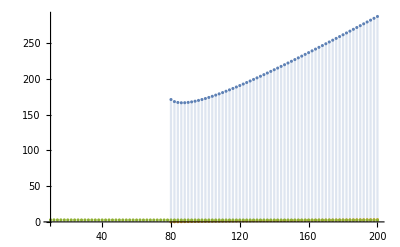

```mathematica
Null
```

```mathematica
Plot[Shalf/]
```

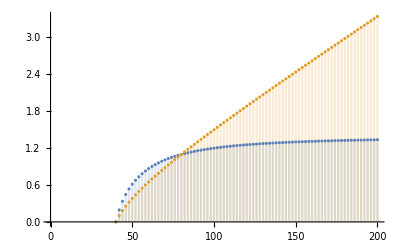

100

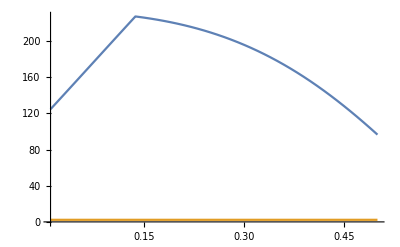

```mathematica
Clear[Γ,q]
n=100
Plot[{
Min[-n Log[w101*w010]-Log[Binomial[n,n/2]],-2n Log[w101*w010/w111/w000]-2Log[Binomial[n,n/2]]]/.{q->2,Γ->0.001}, 1/2 Log[n]},{p,0.01,0.5}, PlotLegends->LineLegend[Automatic,{0,0.001,0.01,0.05,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["I(p,\\Gamma)/N",Magnification->2]},LabelStyle->{FontSize->22}]
```

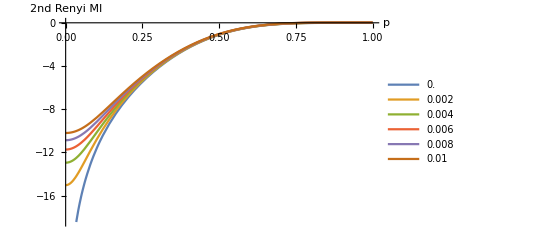

```mathematica
Plot[Evaluate@Table[(-3 Log[w010*w100/w110]-Log[w111]+4Log[w000])/.{q->2,Γ->.0001*g},{g,0,100,20}],{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15]]
```

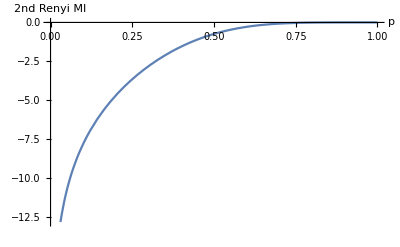

```mathematica
Plot[-2Log[w100*w010/(w110* w000)]/.{q->2,Γ->0},{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15]]
```

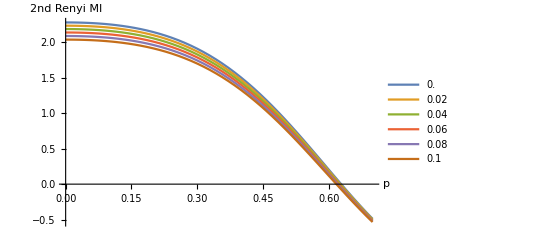

```mathematica
Plot[Evaluate@Table[-2Log[2w010*w101/(w111* w000)]/.{q->2,Γ->.01*g},{g,0,10,2}],{p,0,0.7},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.01*g,{g,0,10,2}],Spacings->0.15]]
```

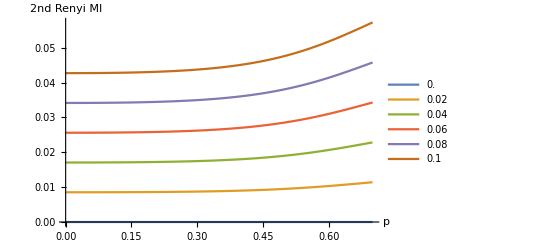

```mathematica
Plot[Evaluate@Table[2Log[w000/ w111]/.{q->2,Γ->.001*g},{g,0,10,2}],{p,0,0.7},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.01*g,{g,0,10,2}],Spacings->0.15]]
```

32

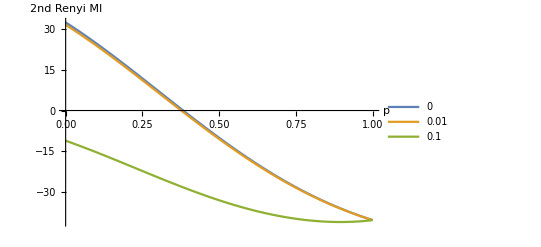

```mathematica
n=32
renyiVol = Plot[{-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0},
-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0.1},
-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0.5}},{Γ,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.01,0.1}]
```

Null

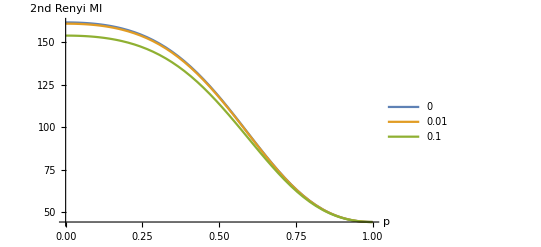

/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_volume.png

```mathematica
n=32
renyiVol = Plot[{-2n Log[w100*w011/(2w111*w000) ]/.{q->2,Γ->0},
-2n Log[w100*w011/(2w111*w000)]/.{q->2,Γ->0.01},
-2n Log[w100*w011/(2w111*w000)]/.{q->2,Γ->0.1}},{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.01,0.1}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_volume.png",Rasterize[renyiVol,ImageResolution->150]]
```

```mathematica
W000[p_,q_,Γ_]:=w3test[1,1,1,q,Γ,p];
W001[p_,q_,Γ_]:=w3test[1,1,-1,q,Γ,p];
W010[p_,q_,Γ_]:=w3test[1,-1,1,q,Γ,p];
W100[p_,q_,Γ_]:=w3test[-1,1,1,q,Γ,p];
W101[p_,q_,Γ_]:=w3test[-1,1,-1,q,Γ,p];
W011[p_,q_,Γ_]:=w3test[1,-1,-1,q,Γ,p];
W110[p_,q_,Γ_]:=w3test[-1,-1,1,q,Γ,p];
W111[p_,q_,Γ_]:=w3test[-1,-1,-1,q,Γ,p];
```

## Null

```mathematica
Null
```